#### 10.04.21 - Расчёт ошибки кумулянта прямоугольного Изинга при разных отношениях сторон

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\user\Documents\Wolfram Mathematica\Проект\Расчёты .nb

```mathematica
data = Import["results.txt", "table"]
```

{{50,0.25,1,0.109901,0.00462847,0.0279148,0.00212686,0.229605},{50,0.5,1,0.141223,0.00422358,0.0374659,0.00187789,0.373811},{50,0.75,1,0.143292,0.0042087,0.0377988,0.00180791,0.386359},{100,0.25,1,0.0890685,0.00405307,0.018081,0.00161062,0.240281},{100,0.5,1,0.115757,0.00358826,0.0261556,0.00130813,0.349347},{100,0.75,1,0.118994,0.00358253,0.0265074,0.00162272,0.375988}}

data[...][1] - L
data[...][2] - CoefXY
data[...][3] - OpenBorderQ (1 - Yes, 0 - No)
data[...][4] - ⟨m2⟩
data[...][5] - σ(m2)
data[...][6] - ⟨m4⟩
data[...][7] - σ(m4)
data[...][8] - U_4

#### Реализация расчёта ошибки:

1. Генерация набора из 1000 значений намагниченностей (второй и четвёртой степени) (средним в распределении является средняя намагниченность, а С.К.О. - её ошибка) и набора кумулянтов из первых двух наборов

```mathematica
dM2 = RandomVariate[NormalDistribution[data[[1]][[4]], data[[1]][[5]]],1000];
dM4 = RandomVariate[NormalDistribution[data[[1]][[6]], data[[1]][[7]]],1000];
dU4 = 1 - dM4 / (3 * dM2^2);
```

Так выглядит гистограмма распределения кумулянта

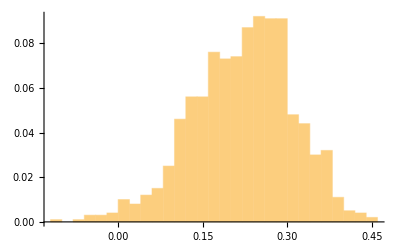

```mathematica
Histogram[dU4, Automatic, "Probability"]
```

На основе гистограммы задаём распределение кумулянта и находит его отклонение

```mathematica
StandardDeviation[HistogramDistribution[dU4]]
```

0.0889934

#### Полуавтоматизированный алгоритм для задания набора точек и их ошибок:

```mathematica
Ls={50,100};
FullData={};
Do[
lData=Select[data, #[[1]]==L&];
line={};
For [i=1, i≤Length[lData],i++,
dM2 = RandomVariate[NormalDistribution[lData[[i]][[4]], lData[[i]][[5]]],1000];
dM4 = RandomVariate[NormalDistribution[lData[[i]][[6]], lData[[i]][[7]]],1000];
dU4 = 1 - dM4 / (3 * dM2^2);
dot={{lData[[i]][[2]], lData[[i]][[8]]},ErrorBar[StandardDeviation[HistogramDistribution[dU4]]]};
AppendTo[line,dot];
];
AppendTo[FullData,line];
,{L,Ls}]
```

```mathematica
Needs["ErrorBarPlots`"]
```

#### График для первых шести расчётов (L=50, 100, AspectRatio=1/4, 1/2 3/4)

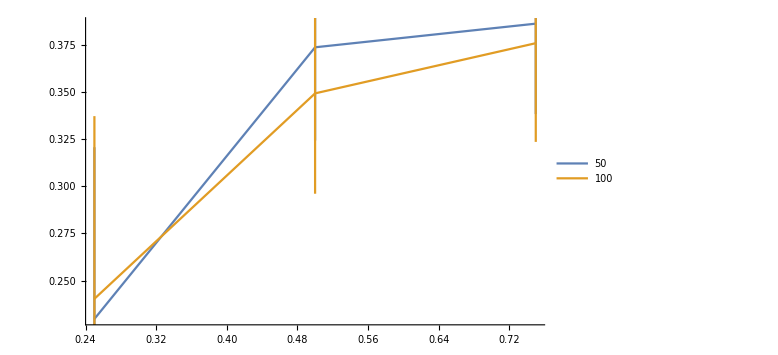

```mathematica
ErrorListPlot[FullData, PlotLegends->Ls, ImageSize->Large, Joined->True]
```

#### Как и ожидалось, погрешности слишком большие -> требуется увеличение времени работы алгоритма